```mathematica
Integrate[c0*(c1(1-Exp[-(t-c2)/c3])),{t,0,t'}]
```

c0 c1 (c3 ⅇ^(c2/c3) (-1+ⅇ^(-t'/c3))+t')

```mathematica
Integrate[c0*(c1(1-Exp[-(t)/c3])),{t,0,t'}]
```

c0 c1 (c3 (-1+ⅇ^(-t'/c3))+t')

```mathematica
Integrate[(c1(1-Exp[-(t)/c3])),{t,0,t'}]
```

c1 (c3 (-1+ⅇ^(-t'/c3))+t')

```mathematica
Integrate[c0*(c1(1-Exp[-(t-t2)/tm])),{t,t1+t2,t'}]
```

c0 c1 (-t1-t2-ⅇ^(-t1/tm) tm+ⅇ^((t2-t')/tm) tm+t')

```mathematica
Integrate[c0*(c1(1-Exp[-(t-t2)/tm])),{t,t2,t'}]
```

c0 c1 (-t2+(-1+ⅇ^((t2-t')/tm)) tm)+c0 c1 t'

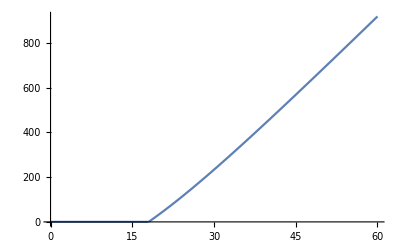

```mathematica
Plot[0.9804 *24.2017 (12* (-Exp[-15/12]+ⅇ^(-(t-3)/12))+(t-3-15))*HeavisideTheta[t-18],{t,0,60}]
```

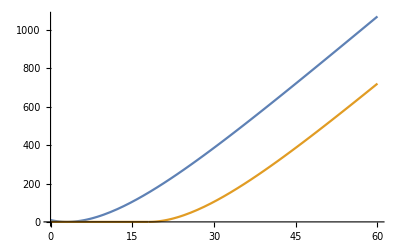

```mathematica
Plot[{0.9804 *24.2017 (-3+ (-1+ⅇ^((3-t)/12))*12)+0.9804 *24.2017*t,0.9804 *24.2017( 12*(-1+ⅇ^(-(t-18)/12))+(t-18))*HeavisideTheta[t-18]},{t,0,60}]
```

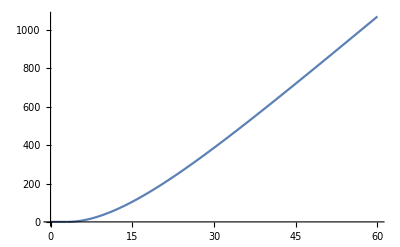

```mathematica
Plot[0.9804 *24.2017( (-3+ (-1+ⅇ^((3-t)/12))*12)+t)*HeavisideTheta[t-3],{t,0,60}]
```

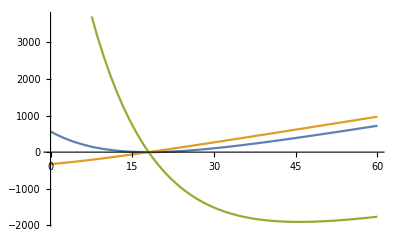

```mathematica
Plot[{0.9804 24.2017 (12 (-1+ⅇ^(-1/12 (t-18)))+t-18),0.9804 24.2017 (12 *0.1*(-1+ⅇ^(-1/12 (t-18)))+t-18),0.9804 24.2017 (12 *10*(-1+ⅇ^(-1/12 (t-18)))+t-18)},{t,0,60}]
```